```mathematica
funcs
equations
state /. t->0
funcs
(ratio[t] /. {ψ[1][t] -> state[[1]], ψ[2][t] -> state[[2]], ψ[3][t] -> state[[3]]}) /. t->10
```

{ψ[1][t],ψ[2][t],ψ[3][t]}

{0.5 Cos[8 t] ψ[3][t]==ⅈ ψ[1]'[t],ψ[2][t]+0.5 Cos[7 t] ψ[3][t]==ⅈ ψ[2]'[t],0.5 Cos[8 t] ψ[1][t]+0.5 Cos[7 t] ψ[2][t]+10 ψ[3][t]==ⅈ ψ[3]'[t],ψ[1][0]==1,ψ[2][0]==0,ψ[3][0]==0}

{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{ψ[1][t],ψ[2][t],ψ[3][t]}

0.345267-1.24671 ⅈ

1.

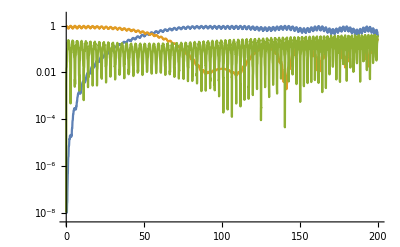

```mathematica
Clear[f, ratio, g, M];


f[t_] := 1*Cos[7t]*(1 - t/100);
g[t_] := 1*Cos[8t]*(t/100);

M = {{0, 0, g[t]}, {0, 1, f[t]}, {g[t], f[t], 10}};

(*ratio[t_] := (ψ[2][t] + .000001)/(ψ[3][t] + .000001)
angle[t_] := ArcTan[Re[ratio[t]], Im[ratio[t]]] + π/2
f[t_] := .5*(*Min[(Abs[ψ[1][t]] + .000001)/(Abs[ψ[2][t]] + .000001), 1]*)Cos[angle[t]]

ratio2[t_] := (ψ[1][t] + .000001)/(ψ[3][t] + .000001)
angle2[t_] := ArcTan[Re[ratio[t]], Im[ratio[t]]] + π/2
g[t_] := -.5*Cos[angle2[t]]*)

Tmax = 200;

Clear[ψ];
ψ0 = {0, 1, 0};
stateFs=Array[ψ[#1][t]&,{Length[ψ0]}];

equations=Flatten@Join[Thread[M.stateFs == ⅈ*D[stateFs,t]],Thread[stateFs==ψ0/.t->0](*, {f[t] == ψ[3][t], f[0] == 0}*)];
funcs = Join[stateFs, {(*f[t]*)}];
state= NDSolveValue[equations,funcs,{t,0,Tmax}];

Max[Table[Abs[state[[2]]]^2, {t, 0, Tmax, Tmax/1000}]]

LogPlot[Evaluate@Table[Max[Abs[state[[i]]]^2, 10^-8], {i, Length[state]}],{t,0,Tmax}, PlotRange->All]

(*Plot[(angle[t] /. {ψ[1][t] -> state[[1]], ψ[2][t] -> state[[2]], ψ[3][t] -> state[[3]]}), {t, 0, Tmax}]
Plot[(f[t] /. {ψ[1][t] -> state[[1]], ψ[2][t] -> state[[2]], ψ[3][t] -> state[[3]]}), {t, 0, Tmax}]*)
```